## 4 cour, 6 group

## -Graphics-

```mathematica
func1[x_] := k*x + b1; 
func2[x_] := a*x^2 + b2*x + c; 
func21[x_] := a1*x^2 + b21*x + c1; 
func31[x_] := Sqrt[R^2 - (x - x01)^2] + y01; 
func4[x_] := α*Cos[β*x + γ];
x0 = 0; 
x1 = 5; 
x2 = 7; 
x3 = 10; 
x4 = 12; 
x5 = 16; 
α = 15; 
β = 2.2; 
γ = 0.05; 
n = Mod[604, 4] + 2;
```

## NULL?

```mathematica
n = Mod[604, 4] + 2
```

2

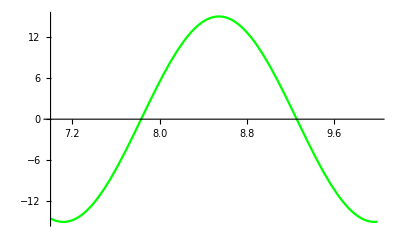

```mathematica
Plot[func4[x],{x,x2,x3},PlotStyle -> RGBColor[0,1,0]]
```

## L4 → L1

```mathematica
currX = x2;

solution = Solve[{func4[currX] == func1[currX],
	D[func4[x],x] == D[func1[x],x] /. {x -> currX}},
	{k,b1}];
	
k = solution⟦1⟧⟦1⟧⟦2⟧//N;
b1 = solution⟦1⟧⟦2⟧⟦2⟧//N;
```

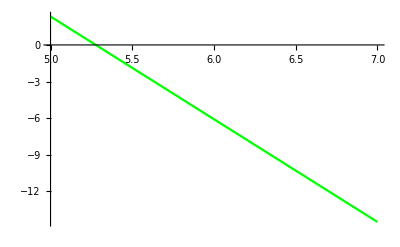

```mathematica
Plot[func1[x],{x,x1,x2},PlotStyle -> RGBColor[0,1,0]]
```

## L1 → L2

```mathematica
currX = x1;
c = 0;

solution = Solve[{func1[currX] == func2[currX],
	D[func1[x],x] == D[func2[x],x] /. {x -> currX}},
	{a,b2}];
	
a = solution⟦1⟧⟦1⟧⟦2⟧//N;
b2 = solution⟦1⟧⟦2⟧⟦2⟧//N;
```

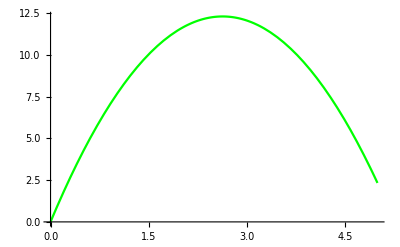

```mathematica
Plot[func2[x],{x,x0,x1},PlotStyle -> RGBColor[0,1,0]]
```

## L4 → L3

```mathematica
R = 5;
currX = x3;

solution = Solve[{func4[currX] == func31[currX],
	D[func4[x],x] == D[func31[x],x] /. {x -> currX}},
	{x01,y01}];
	
x01 = solution⟦1⟧⟦1⟧⟦2⟧//N;
y01 = solution⟦1⟧⟦2⟧⟦2⟧//N;
```

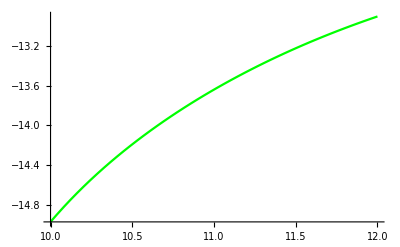

```mathematica
Plot[func31[x],{x,x3,x4},PlotStyle -> RGBColor[0,1,0]]
```

## L3 → L2

```mathematica
c1 = 0;
currX = x4;

solution = Solve[{func31[currX] == func21[currX],
	D[func31[x],x] == D[func21[x],x] /. {x -> currX}},
	{a1,b21},Reals]
	
a1 = solution⟦1⟧⟦1⟧⟦2⟧//N;
b21 = solution⟦1⟧⟦2⟧⟦2⟧//N;
```

{{a1→0.136311,b21→-2.71094}}

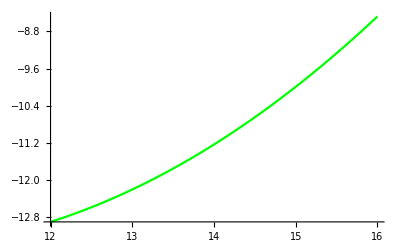

```mathematica
Plot[func21[x],{x,x4,x5},PlotStyle -> RGBColor[0,1,0]]
```

## Final plot

```mathematica
Dfunc1 = D[func1[x],x];
Dfunc2 = D[func2[x],x];
Dfunc21 = D[func21[x],x];
Dfunc31 = D[func31[x],x];
Dfunc4 = D[func4[x],x];
```

```mathematica
Show[Plot[func2[x],{x,x0,x1},PlotStyle -> RGBColor[0,1,0],PlotLegends->{"Функция"}],
	Plot[func1[x],{x,x1,x2},PlotStyle -> RGBColor[0,1,0]],
	Plot[func4[x],{x,x2,x3},PlotStyle -> RGBColor[0,1,0]],
	Plot[func31[x],{x,x3,x4},PlotStyle -> RGBColor[0,1,0]],
	Plot[func21[x],{x,x4,x5},PlotStyle -> RGBColor[0,1,0]],
	Plot[Dfunc2,{x,x0,x1},PlotStyle -> RGBColor[0,0,(15/255)],PlotLegends->{"Проивзодная"}],
	Plot[Dfunc1,{x,x1,x2},PlotStyle -> RGBColor[0,0,(15/255)],PlotRange -> All],
	Plot[Dfunc4,{x,x2,x3},PlotStyle -> RGBColor[0,0,(15/255)]],
	Plot[Dfunc31,{x,x3,x4},PlotStyle -> RGBColor[0,0,(15/255)]],
	Plot[Dfunc21,{x,x4,x5},PlotStyle -> RGBColor[0,0,(15/255)]],
	ListPlot[{{x1,func2[x1]},{x2,func1[x2]},{x3,func4[x3]},{x4,func31[x4]}}->{"x1","x2","x3","x4"}],
	PlotRange->{{x0,x5},{-60,60}},AxesStyle -> {Black,Black}, AxesLabel -> {x,y},Ticks -> {{0,4,8,12},{-60,-40,-20,0,20,40,60}},GridLines -> {None,{-40,40}},AspectRatio->1/0.95]
```

-Graphics-

```mathematica
Animate[Show[Plot[func2[x],{x,x0*t,x1*t}],
	Plot[func1[x],{x,x1*t,x2*t},PlotStyle -> Yellow],
	Plot[func4[x],{x,x2*t,x3*t},PlotStyle -> Red],
	Plot[func31[x],{x,x3*t,x4*t},PlotStyle -> Green],
	Plot[func21[x],{x,x4*t,x5*t},PlotStyle -> Purple],
	ListPlot[{{x1,func2[x1]},{x2,func1[x2]},{x3,func4[x3]},{x4,func31[x4]}}],
	PlotRange->{{x0,x5},{-20,20}}, AxesLabel -> {x,y}],
	{t,0.00001,1,0.01},DisplayAllSteps->True, AnimationRunning -> False]
```